```mathematica
Odd = {0.00341978, 0.0029875, 0.00258646, 0.00214488, 0.00167539}
```

{0.00341978,0.0029875,0.00258646,0.00214488,0.00167539}

```mathematica
Even = {0.00115303, 0.00138656, 0.001624, 0.00186617, 0.00214918 }
```

{0.00115303,0.00138656,0.001624,0.00186617,0.00214918}

```mathematica
Rho = Table[Even[[i]]+Odd[[i]], {i,1,5}]
```

{0.00457281,0.00437406,0.00421046,0.00401105,0.00382457}

```mathematica
DeltaRho = Table[(Rho[[i]]-Rho[[1]])/(0.6666666^2+2*0.33333333^2), {i,1,5}]
```

```mathematica
{0.,-0.00019875000000000014,-0.00036235,-0.000561599999999997,-0.0007482399999999998}
```

```mathematica
Mu = {0.0, 0.140, 0.200, 0.245, 0.285};
```

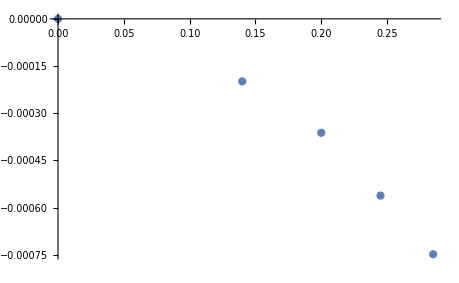

```mathematica
Plt = ListPlot[Table[{Mu[[j]], DeltaRho[[j]]},{j,1,5}]]
```